# Precession of magnetar

## 1. The dynamics of magnetar precession

## Time scale estimation

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;
c=29979245800.0;
Ms=1.988409870698051*10^33;
km=10^5;
R=10*km;
M=1.4*Ms;
Is=2/5*M*R^2;
P=1;k=0.6;B=10^14;
ω=(2 π)/P;
m=(B R^3)/2;
τc=(3 c^3 Is)/((2 m^2) ω^2)
τa=(2 R ω τc)/((3 k) c)
ϵp=(3 B^2 R^5)/(20 (Is c^2))
```

4.55982×10^11

1.06185×10^8

1.49884×10^-9

```mathematica
I1=I0;I2=I1 (1+ϵ1);I3=I1 (1+ϵ);
Ib=DiagonalMatrix[{I1,I2,I3}];
Ω={ω0*u1[t], ω0*u2[t], ω0*u3[t]};
p={m*Sin[χ]Cos[η],m Sin[χ]Sin[η],m Cos[χ]};
T1=(2 ω0^2*u[t]^2)/(3 c^3)Cross[Cross[Ω,p],p];
```

## spindown term

```mathematica
cosα=μ1*Sin[θ0]*JacobiCN[τ,m]+μ2*Sin[θ0]*(1+δ)^(1/2)JacobiSN[τ,m]+μ3*Cos[θ0]*JacobiDN[τ,m]
```

μ3 Cos[θ0] JacobiDN[τ,m]+μ1 JacobiCN[τ,m] Sin[θ0]+√(1+δ) μ2 JacobiSN[τ,m] Sin[θ0]

```mathematica
core=Expand[cosα^2]
```

μ3^2 Cos[θ0]^2 JacobiDN[τ,m]^2+2 μ1 μ3 Cos[θ0] JacobiCN[τ,m] JacobiDN[τ,m] Sin[θ0]+2 √(1+δ) μ2 μ3 Cos[θ0] JacobiDN[τ,m] JacobiSN[τ,m] Sin[θ0]+μ1^2 JacobiCN[τ,m]^2 Sin[θ0]^2+2 √(1+δ) μ1 μ2 JacobiCN[τ,m] JacobiSN[τ,m] Sin[θ0]^2+μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2+δ μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2

```mathematica
Integrate[JacobiDN[τ,m]^2,τ] μ3^2 Cos[θ0]^2
```

(μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m] JacobiDN[τ,m])/(√(1-m JacobiSN[τ,m]^2))

```mathematica
s1=μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m]
```

μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m]

```mathematica
s2=Integrate[2 μ1 μ3 Cos[θ0] JacobiCN[τ,m] JacobiDN[τ,m] Sin[θ0],τ]
```

μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
s3=Integrate[2 √(1+δ) μ2 μ3 Cos[θ0] JacobiDN[τ,m] JacobiSN[τ,m] Sin[θ0],τ]
```

-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]

```mathematica
s4=Simplify[Integrate[μ1^2 JacobiCN[τ,m]^2 Sin[θ0]^2,τ]]
```

μ1^2 (τ-τ/m+(EllipticE[JacobiAmplitude[τ,m],m] (-1+1/m+JacobiCN[τ,m]^2))/(JacobiDN[τ,m] √(1-m JacobiSN[τ,m]^2))) Sin[θ0]^2

```mathematica
s4=Expand[Simplify[μ1^2 (τ-τ/m+(EllipticE[JacobiAmplitude[τ,m],m] (JacobiDN[τ,m]^2/m))/(JacobiDN[τ,m] JacobiDN[τ,m])) Sin[θ0]^2]]
```

μ1^2 τ Sin[θ0]^2-(μ1^2 τ Sin[θ0]^2)/m+(μ1^2 EllipticE[JacobiAmplitude[τ,m],m] Sin[θ0]^2)/m

```mathematica
s5=Integrate[2 √(1+δ) μ1 μ2 JacobiCN[τ,m] JacobiSN[τ,m] Sin[θ0]^2,τ]
```

-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m

```mathematica
s6=Simplify[Integrate[μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2,τ]]
```

(μ2^2 (τ JacobiDN[τ,m]-EllipticE[JacobiAmplitude[τ,m],m] √(1-m JacobiSN[τ,m]^2)) Sin[θ0]^2)/(m JacobiDN[τ,m])

```mathematica
s6=Simplify[(μ2^2 (τ JacobiDN[τ,m]-EllipticE[JacobiAmplitude[τ,m],m]JacobiDN[τ,m] ) Sin[θ0]^2)/(m JacobiDN[τ,m])]
```

(μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2)/m

```mathematica
s7=δ*s6
```

(δ μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2)/m

```mathematica
s=s1+s2+s3+s4+s5+s6+s7
```

μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m]+μ1^2 τ Sin[θ0]^2-(μ1^2 τ Sin[θ0]^2)/m+(μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2)/m+(δ μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2)/m+(μ1^2 EllipticE[JacobiAmplitude[τ,m],m] Sin[θ0]^2)/m-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]+μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+√(1+δ) μ2 μ3 Sin[2 θ0]

```mathematica
sol1=Simplify[Coefficient[s,EllipticE[JacobiAmplitude[τ,m],m]]]EllipticE[JacobiAmplitude[τ,m],m]
```

EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)

```mathematica
sol2=Simplify[Coefficient[s,τ]]*τ
```

(((-1+m) μ1^2+(1+δ) μ2^2) τ Sin[θ0]^2)/m

```mathematica
sol3=Simplify[Coefficient[s,JacobiDN[τ,m]]]JacobiDN[τ,m]
sol4=Simplify[Coefficient[s,JacobiCN[τ,m]]]JacobiCN[τ,m]
sol5=Simplify[Coefficient[s,JacobiSN[τ,m]]]JacobiSN[τ,m]
```

-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m

-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]

μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
sol6=-s/.τ-> 0
```

(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+√(1+δ) μ2 μ3 Sin[2 θ0]

```mathematica
sol=sol1+sol2+sol3+sol4+sol5+sol6
```

(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+(((-1+m) μ1^2+(1+δ) μ2^2) τ Sin[θ0]^2)/m-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)+√(1+δ) μ2 μ3 Sin[2 θ0]-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]+μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
a=Simplify[(sol/.{τ-> 4*EllipticK[m]})/(4*EllipticK[m])]
```

1/(m EllipticK[m])(((-1+m) μ1^2+(1+δ) μ2^2) EllipticK[m] Sin[θ0]^2+EllipticE[m] (m μ3^2 Cos[θ0]^2+(μ1^2-(1+δ) μ2^2) Sin[θ0]^2))

```mathematica
b=sol/.{τ-> 0}
```

0

```mathematica
Simplify[Integrate[(μ1*Sin[θ0]*Cos[τ]+μ3*Cos[θ0])^2,τ]]
```

1/4 (μ1^2 τ+2 μ3^2 τ-(μ1^2-2 μ3^2) τ Cos[2 θ0]+8 μ1 μ3 Cos[θ0] Sin[θ0] Sin[τ]+μ1^2 Sin[θ0]^2 Sin[2 τ])

```mathematica
Spindown[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
L1=Sin[θ0]*JacobiCN[ωp*t1,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t1,m];
L3=Cos[θ0]*JacobiDN[ωp*t1,m];
N0=(k1 μ^2*ω0^2)/(c^3 I0);
l1=N0*k2*t;
l2=-N0*NIntegrate[(L1*μ1+L2*μ2+L3*μ3)^2,{t1,0,t},WorkingPrecision->10];
l=l1+l2;
l

]
```

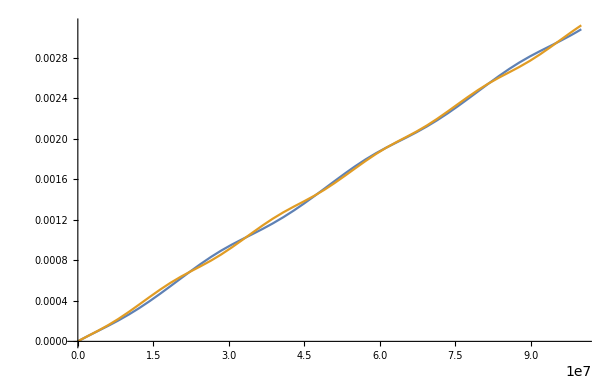

```mathematica
Plot[{Spindown[10^-7,1,45/180*π,45/180*π,15/180*π,5*10^14,2,1,2,t],Spindown[10^-7,0,45/180*π,45/180*π,15/180*π,5*10^14,2,1,2,t]},{t,0,10^8}]
```

```mathematica
Spindown1[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
(*L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];*)
N0=(k1 μ^2*ω0^2)/(c^3 I0);
l1=N0*k2*t;
τ=ωp*t;
l2=-N0/ωp*(EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)+(((-1+m) μ1^2+(1+δ) μ2^2) τ Sin[θ0]^2)/m-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]+1/m(2 √(1+δ) μ1 μ2 Sin[θ0]^2+m √(1+δ) μ2 μ3 Sin[2 θ0]));
l=l1+l2;
l

]
```

```mathematica
yr=31557600.0
```

3.15576×10^7

```mathematica
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
T1=T;
time=logspace[0,Log[10,3*yr],1000];
down1=Spindown1[10^-7,1,45/180*π,45/180*π,15/180*π,5*10^14,2,1,2,time];
down2=Spindown1[10^-7,1,45/180*π,45/180*π,15/180*π,5*10^14,2,2/3,1,time];
```

## Biaxial case

```mathematica
Spindown2[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
(*L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];*)
N0=(k1 μ^2*ω0^2)/(c^3 I0);
l1=N0*k2*t;
τ=ωp*t;
l2=-N0/ωp*(1/4 (μ1^2 τ+2 μ3^2 τ-(μ1^2-2 μ3^2) τ Cos[2 θ0]+8 μ1 μ3 Cos[θ0] Sin[θ0] Sin[τ]+μ1^2 Sin[θ0]^2 Sin[2 τ]));
l=l1+l2;
l

]
```

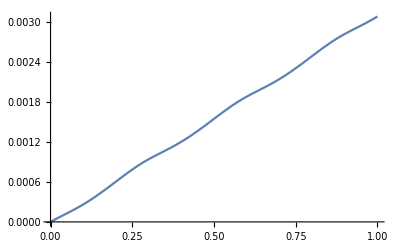

```mathematica
Plot[{Spindown1[10^-7,1,45/180*π,45/180*π,15/180*π,5*10^14,2,1,2,t]},{t,0,10^8}]
time=logspace[0,Log[10,3*yr],1000];
down3=Spindown2[10^-7,0,45/180*π,0,15/180*π,5*10^14,2,1,2,time];
down4=Spindown2[10^-7,0,45/180*π,0,15/180*π,5*10^14,2,2/3,1,time];
```

```mathematica
data=Transpose@{time,down4,down3,down2,down1};
SetDirectory[NotebookDirectory[]];
Export["spindown.dat",data];
```

## Geometric timing residuals

```mathematica
M=EulerMatrix[{ϕ,θ,ψ},{3,1,3}];
μ={μ1,μ2,μ3};
μM=M.μ
```

{μ3 Sin[θ] Sin[ϕ]+μ2 (-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ])+μ1 (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]),-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]),μ3 Cos[θ]+μ2 Cos[ψ] Sin[θ]+μ1 Sin[θ] Sin[ψ]}

```mathematica
μX=μM[[1]]
μY=μM[[2]]
```

μ3 Sin[θ] Sin[ϕ]+μ2 (-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ])+μ1 (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ])

-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])

```mathematica
ArcTan[μY/μX]
```

ArcTan[(-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]))/(μ3 Sin[θ] Sin[ϕ]+μ2 (-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ])+μ1 (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]))]

```mathematica
y=Coefficient[-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]),Sin[ϕ]]
```

μ1 Cos[ψ]-μ2 Sin[ψ]

```mathematica
x=Coefficient[-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]),Cos[ϕ]]
```

μ2 Cos[θ] Cos[ψ]-μ3 Sin[θ]+μ1 Cos[θ] Sin[ψ]

```mathematica
tanϕ=y/x
```

(μ1 Cos[ψ]-μ2 Sin[ψ])/(μ2 Cos[θ] Cos[ψ]-μ3 Sin[θ]+μ1 Cos[θ] Sin[ψ])

```mathematica
Coefficient[-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]),Cos[ϕ]]
```

μ2 Cos[θ] Cos[ψ]-μ3 Sin[θ]+μ1 Cos[θ] Sin[ψ]

```mathematica
Coefficient[-μ3 Cos[ϕ] Sin[θ]+μ1 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])+μ2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]),Sin[ϕ]]
```

μ1 Cos[ψ]-μ2 Sin[ψ]

```mathematica
Coefficient[μ3 Sin[θ] Sin[ϕ]+μ2 (-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ])+μ1 (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]),Sin[ϕ]]
```

-μ2 Cos[θ] Cos[ψ]+μ3 Sin[θ]-μ1 Cos[θ] Sin[ψ]

```mathematica
Coefficient[μ3 Sin[θ] Sin[ϕ]+μ2 (-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ])+μ1 (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]),Cos[ϕ]]
```

μ1 Cos[ψ]-μ2 Sin[ψ]

```mathematica
ψ=π/2-ωp*t;
a=μ1*Cos[ψ]
b=-μ3 Sin[θ]+μ1 Cos[θ] Sin[ψ]
```

μ1 Sin[t ωp]

μ1 Cos[θ] Cos[t ωp]-μ3 Sin[θ]

```mathematica
FullSimplify[(D[a,t]b-D[b,t]a)/(a^2+b^2)/ωp]-1/Cos[θ]
```

-Sec[θ]+(μ1 (μ1 Cos[θ]-μ3 Cos[t ωp] Sin[θ]))/((μ1 Cos[θ] Cos[t ωp]-μ3 Sin[θ])^2+μ1^2 Sin[t ωp]^2)

```mathematica
Simplify[μ1 (μ1 Cos[θ]-μ3 Cos[t ωp] Sin[θ])*Cos[θ]-((μ1 Cos[θ] Cos[t ωp]-μ3 Sin[θ])^2+μ1^2 Sin[t ωp]^2)]
```

μ1 μ3 Cos[θ] Cos[t ωp] Sin[θ]-μ3^2 Sin[θ]^2-μ1^2 Sin[t ωp]^2+μ1^2 Cos[θ]^2 Sin[t ωp]^2

```mathematica
ArcCot[1/8.0]
```

1.44644

```mathematica
N[1.446441332248135/°]
```

82.875

## Timing residuals

```mathematica
Remove["Global`*"]
residual1[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,t_]:=Module[{ΔP,ΔPd},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
I0=10^45;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
tage=0.11*10^6*3.145*10^7;


τrad=(3 c^3 I0)/(2 μ^2 ω0^2);
ΔP1=-ϵ*Sin[θ0]*P*((μ1^2 Sin[θ0] Sin[ωp*t]^2+μ3^2 Sin[θ0]-μ1*μ3 Cos[θ0]Cos[ωp*t])/((μ1*Cos[θ0]Cos[ωp *t]-μ3*Sin[θ0])^2+μ1^2 Sin[ωp*t]^2));
ΔP2=(-3*k1*P)/(2*τrad ωp)(1/2 Sin[2*χ]Sin[2*θ0]Sin[ωp*t]+1/4 Sin[θ0]^2 Sin[χ]^2 Sin[2ωp*t]);
ΔP1d=D[-ϵ*Sin[θ0]*P*((μ1^2 Sin[θ0] Sin[ωp*t1]^2+μ3^2 Sin[θ0]-μ1*μ3 Cos[θ0]Cos[ωp*t1])/((μ1*Cos[θ0]Cos[ωp *t1]-μ3*Sin[θ0])^2+μ1^2 Sin[ωp*t1]^2)),t1]/.{t1->t};
ΔP2d=D[(-3*k1*P)/(2*τrad ωp)(1/2 Sin[2*χ]Sin[2*θ0]Sin[ωp*t1]+1/4 Sin[θ0]^2 Sin[χ]^2 Sin[2ωp*t1]),t1]/.{t1->t};
ΔP=ΔP1+ΔP2;
ΔPd=ΔP2d+ΔP1d;

{ΔP,ΔPd}]
period1[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_]:=Module[{ΔP,ΔPd},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
I0=10^45;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
tage=0.11*10^6*3.145*10^7;
T=2*π*I3/(ϵ L*Cos[θ0]);
{T}]
```

```mathematica
Remove["Global`*"]
residual1[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,t_]:=Module[{ΔP,ΔPd},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
I0=10^45;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
tage=0.11*10^6*3.145*10^7;


τrad=(3 c^3 I0)/(2 μ^2 ω0^2);
ΔP1=-ϵ*Sin[θ0]*P*((μ1^2 Sin[θ0] Sin[ωp*t]^2+μ3^2 Sin[θ0]-μ1*μ3 Cos[θ0]Cos[ωp*t])/((μ1*Cos[θ0]Cos[ωp *t]-μ3*Sin[θ0])^2+μ1^2 Sin[ωp*t]^2));
ΔP2=(-3*k1*P)/(2*τrad ωp)(1/2 Sin[2*χ]Sin[2*θ0]Sin[ωp*t]+1/4 Sin[θ0]^2 Sin[χ]^2 Sin[2ωp*t]);
ΔP1d=D[-ϵ*Sin[θ0]*P*((μ1^2 Sin[θ0] Sin[ωp*t1]^2+μ3^2 Sin[θ0]-μ1*μ3 Cos[θ0]Cos[ωp*t1])/((μ1*Cos[θ0]Cos[ωp *t1]-μ3*Sin[θ0])^2+μ1^2 Sin[ωp*t1]^2)),t1]/.{t1->t};
ΔP2d=D[(-3*k1*P)/(2*τrad ωp)(1/2 Sin[2*χ]Sin[2*θ0]Sin[ωp*t1]+1/4 Sin[θ0]^2 Sin[χ]^2 Sin[2ωp*t1]),t1]/.{t1->t};
(*ΔP=ΔP1+ΔP2;
ΔPd=ΔP2d+ΔP1d;*)

{ΔP1}]
```

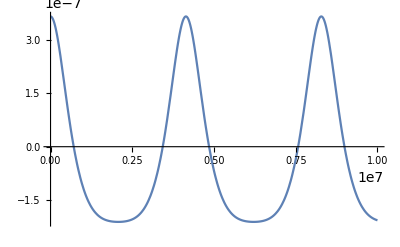

```mathematica
ϵ=5*10^-7;
δ=0;
χ=45/180*π;
η=0;
θ0=15/180*π;
B=2*10^14;
P=2;
k1=1;
Plot[residual1[ϵ,δ,χ,η,θ0,B,P,k1,t],{t,0,10^7}]
```

```mathematica
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
ϵ=5*10^-7;
δ=0;
χ=45/180*π;
η=0;
θ0=15/180*π;
B=2*10^14;
P=2;
k1=1;
T1=period1[ϵ,δ,χ,η,θ0,B,P,k1];
time=linearspace[0,4*T1,500];
ppdot1=residual1[ϵ,δ,χ,η,θ0,B,P,k1,time];
(*Plot[{residual1[5*10^-7,0,45/180*π,0,15/180*π,2*10^14,2,1,t],residual1[5*10^-7,0,45/180*π,0,5/180*π,2*10^14,2,1,t],residual1[5*10^-7,0,85/180*π,0,15/180*π,2*10^14,2,1,t]},{t,0,2*10^7},PlotPoints->600,PlotRange->All]*)
data1=Transpose@{Flatten[time],Flatten[ppdot1[[1]]],
Flatten[ppdot1[[2]]]};
SetDirectory[NotebookDirectory[]];
Export["timing1.dat",data1];
```

```mathematica
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
ϵ=5*10^-7;
δ=0;
χ=45/180*π;
η=0;
θ0=5/180*π;
B=2*10^14;
P=2;
k1=1;
T1=period1[ϵ,δ,χ,η,θ0,B,P,k1];
time=linearspace[0,4*T1,500];
ppdot1=residual1[ϵ,δ,χ,η,θ0,B,P,k1,time];
(*Plot[{residual1[5*10^-7,0,45/180*π,0,15/180*π,2*10^14,2,1,t],residual1[5*10^-7,0,45/180*π,0,5/180*π,2*10^14,2,1,t],residual1[5*10^-7,0,85/180*π,0,15/180*π,2*10^14,2,1,t]},{t,0,2*10^7},PlotPoints->600,PlotRange->All]*)
data2=Transpose@{Flatten[time],Flatten[ppdot1[[1]]],
Flatten[ppdot1[[2]]]};
SetDirectory[NotebookDirectory[]];
Export["timing2.dat",data2];
```

```mathematica
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
ϵ=5*10^-7;
δ=0;
χ=85/180*π;
η=0;
θ0=15/180*π;
B=2*10^14;
P=2;
k1=1;
T1=period1[ϵ,δ,χ,η,θ0,B,P,k1];
time=linearspace[0,4*T1,500];
ppdot1=residual1[ϵ,δ,χ,η,θ0,B,P,k1,time];
(*Plot[{residual1[5*10^-7,0,45/180*π,0,15/180*π,2*10^14,2,1,t],residual1[5*10^-7,0,45/180*π,0,5/180*π,2*10^14,2,1,t],residual1[5*10^-7,0,85/180*π,0,15/180*π,2*10^14,2,1,t]},{t,0,2*10^7},PlotPoints->600,PlotRange->All]*)
data3=Transpose@{Flatten[time],Flatten[ppdot1[[1]]],
Flatten[ppdot1[[2]]]};
SetDirectory[NotebookDirectory[]];
Export["timing3.dat",data3];
```

## geometric term of triaxial NS

```mathematica
residual2[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,t_]:=Module[{ΔP},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
x=-μ2 JacobiCN[t ωp,m]+√(1+δ) μ1 JacobiSN[t ωp,m];
y=μ1 Cos[θ0] JacobiCN[t ωp,m] JacobiDN[t ωp,m]+√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m] JacobiSN[t ωp,m]+μ3 (1+δ JacobiSN[t ωp,m]^2) Sin[θ0];
dx=ωp JacobiDN[t ωp,m] (√(1+δ) μ1 JacobiCN[t ωp,m]+μ2 JacobiSN[t ωp,m]);
dy=ωp (-m μ1 Cos[θ0] JacobiCN[t ωp,m]^2 JacobiSN[t ωp,m]-μ1 Cos[θ0] JacobiDN[t ωp,m]^2 JacobiSN[t ωp,m]+JacobiCN[t ωp,m] (√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m]^2-m √(1+δ) μ2 Cos[θ0] JacobiSN[t ωp,m]^2+2 δ μ3 JacobiDN[t ωp,m] JacobiSN[t ωp,m] Sin[θ0]));
term=(dx*y-x*dy)/(x^2+y^2);
ΔP1=(term/ωp-Sqrt[1+δ]/(Cos[θ0](1+δ JacobiSN[ωp*t,m]^2)))(ϵ *Cos[θ0]P)/Sqrt[1+δ];
ΔP=ΔP1;
{ΔP}]
```

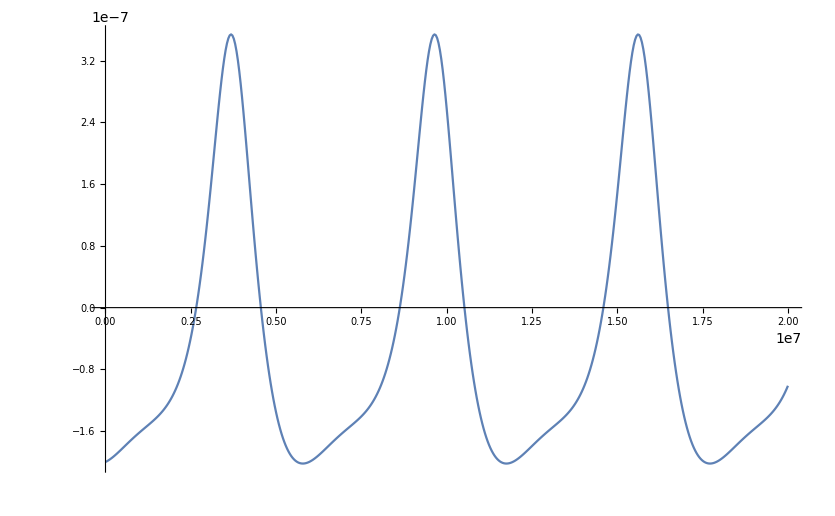

```mathematica
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
time=linearspace[0,2*10^7,500];
delta=residual2[5*10^-7,1,45/180*π,45/180*π,15/180*π,2*10^14,2,1,time];
list=Transpose@{Flatten[time],Flatten[delta]};
ListPlot[list,Joined->True,PlotRange->All]
```

```mathematica
x=-μ2 JacobiCN[t ωp,m]+√(1+δ) μ1 JacobiSN[t ωp,m];
y=μ1 Cos[θ0] JacobiCN[t ωp,m] JacobiDN[t ωp,m]+√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m] JacobiSN[t ωp,m]+μ3 (1+δ JacobiSN[t ωp,m]^2) Sin[θ0];
dx=Simplify[D[x,t]]
dy=Simplify[D[y,t]]
```

ωp JacobiDN[t ωp,m] (√(1+δ) μ1 JacobiCN[t ωp,m]+μ2 JacobiSN[t ωp,m])

ωp (-m μ1 Cos[θ0] JacobiCN[t ωp,m]^2 JacobiSN[t ωp,m]-μ1 Cos[θ0] JacobiDN[t ωp,m]^2 JacobiSN[t ωp,m]+JacobiCN[t ωp,m] (√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m]^2-m √(1+δ) μ2 Cos[θ0] JacobiSN[t ωp,m]^2+2 δ μ3 JacobiDN[t ωp,m] JacobiSN[t ωp,m] Sin[θ0]))

```mathematica
yy=-m μ1 Cos[θ0] JacobiCN[t ωp,m]^2 JacobiSN[t ωp,m]-μ1 Cos[θ0] JacobiDN[t ωp,m]^2 JacobiSN[t ωp,m]+JacobiCN[t ωp,m] (√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m]^2-m √(1+δ) μ2 Cos[θ0] JacobiSN[t ωp,m]^2+2 δ μ3 JacobiDN[t ωp,m] JacobiSN[t ωp,m] Sin[θ0])
```

-m μ1 Cos[θ0] JacobiCN[t ωp,m]^2 JacobiSN[t ωp,m]-μ1 Cos[θ0] JacobiDN[t ωp,m]^2 JacobiSN[t ωp,m]+JacobiCN[t ωp,m] (√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m]^2-m √(1+δ) μ2 Cos[θ0] JacobiSN[t ωp,m]^2+2 δ μ3 JacobiDN[t ωp,m] JacobiSN[t ωp,m] Sin[θ0])

```mathematica
Simplify[Coefficient[yy,μ1]]
```

-Cos[θ0] (m JacobiCN[t ωp,m]^2+JacobiDN[t ωp,m]^2) JacobiSN[t ωp,m]

```mathematica
Simplify[Coefficient[yy,μ2]]
```

√(1+δ) Cos[θ0] JacobiCN[t ωp,m] (JacobiDN[t ωp,m]^2-m JacobiSN[t ωp,m]^2)

```mathematica
Simplify[Coefficient[yy,μ3]]
```

2 δ JacobiCN[t ωp,m] JacobiDN[t ωp,m] JacobiSN[t ωp,m] Sin[θ0]

```mathematica
dN=2b3*Sin[θ0]δ JacobiSN[ωp *t,m]JacobiCN[ωp t,m]JacobiDN[ωp t,m]+b2*Cos[θ0]JacobiCN[ωp t,m](JacobiDN[ωp t,m]^2-m*JacobiSN[ωp *t,m]^2)Sqrt[1+δ]-b1 Cos[θ0](JacobiDN[ωp t,m]^2+m*JacobiCN[ωp *t,m]^2);
dD=-b2 JacobiSN[ωp t,m]JacobiDN[ωp t,m]-b1 JacobiCN[ωp t,m]JacobiDN[ωp t,m]Sqrt[1+δ];
```

```mathematica
JacobiDN[t ωp,m] (√(1+δ) μ1 JacobiCN[t ωp,m]+μ2 JacobiSN[t ωp,m])
```

JacobiDN[t ωp,m] (√(1+δ) μ1 JacobiCN[t ωp,m]+μ2 JacobiSN[t ωp,m])

## Spindown term

```mathematica
-(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+(EllipticE[m]/EllipticK[m] τ-EllipticE[JacobiAmplitude[τ,m],m]) (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)-√(1+δ) μ2 μ3 Sin[2 θ0]+√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]-μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]
```

-(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+(-EllipticE[JacobiAmplitude[τ,m],m]+(τ EllipticE[m])/EllipticK[m]) (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)-√(1+δ) μ2 μ3 Sin[2 θ0]+√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]-μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
Remove["Global`*"]
constant[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_]:=Module[{const},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
τrad=(3 c^3 I0)/(2 μ^2 ω0^2);

const=N[Integrate[(3*k1*P)/(2*τrad ωp)(-(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+(2 √(1+δ) μ1 μ2 JacobiDN[τ1,m] Sin[θ0]^2)/m+(-EllipticE[JacobiAmplitude[τ1,m],m]+(τ1* EllipticE[m])/EllipticK[m]) (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)-√(1+δ) μ2 μ3 Sin[2 θ0]+√(1+δ) μ2 μ3 JacobiCN[τ1,m] Sin[2 θ0]-μ1 μ3 JacobiSN[τ1,m] Sin[2 θ0]),{τ1,0,4*EllipticK[m]}]]/(4*EllipticK[m]);
{const}]
aa=constant[5*10^-7,1,45/180*π,45/180*π,5/180*π,2*10^14,2,1];
```

```mathematica
aa
```

{-5.24259×10^-7}

```mathematica
Remove["Global`*"]
aa=-5.24259*10^-7;
residual3[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,t1_]:=Module[{ΔP,ΔPd},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
x=-μ2 JacobiCN[t ωp,m]+√(1+δ) μ1 JacobiSN[t ωp,m];
y=μ1 Cos[θ0] JacobiCN[t ωp,m] JacobiDN[t ωp,m]+√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m] JacobiSN[t ωp,m]+μ3 (1+δ JacobiSN[t ωp,m]^2) Sin[θ0];
dx=ωp JacobiDN[t ωp,m] (√(1+δ) μ1 JacobiCN[t ωp,m]+μ2 JacobiSN[t ωp,m]);
dy=ωp (-m μ1 Cos[θ0] JacobiCN[t ωp,m]^2 JacobiSN[t ωp,m]-μ1 Cos[θ0] JacobiDN[t ωp,m]^2 JacobiSN[t ωp,m]+JacobiCN[t ωp,m] (√(1+δ) μ2 Cos[θ0] JacobiDN[t ωp,m]^2-m √(1+δ) μ2 Cos[θ0] JacobiSN[t ωp,m]^2+2 δ μ3 JacobiDN[t ωp,m] JacobiSN[t ωp,m] Sin[θ0]));
term=(dx*y-x*dy)/(x^2+y^2);
ΔP1=(term/ωp-Sqrt[1+δ]/(Cos[θ0](1+δ JacobiSN[ωp*t,m]^2)))(ϵ *Cos[θ0]P)/Sqrt[1+δ]/.{t-> t1};
ΔPd1=D[ΔP1,t]/.{t-> t1};
τrad=(3 c^3 I0)/(2 μ^2 ω0^2);
τ=ωp*t;
ΔP2=(3*k1*P)/(2*τrad ωp)(-(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+(-EllipticE[JacobiAmplitude[τ,m],m]+(τ EllipticE[m])/EllipticK[m]) (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)-√(1+δ) μ2 μ3 Sin[2 θ0]+√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]-μ1 μ3 JacobiSN[τ,m] Sin[2 θ0])/.{t->t1};
ΔPd2=D[(3*k1*P)/(2*τrad ωp)(-(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/m+(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+(-EllipticE[JacobiAmplitude[τ,m],m]+(τ EllipticE[m])/EllipticK[m]) (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)-√(1+δ) μ2 μ3 Sin[2 θ0]+√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]-μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]),t]/.{t->t1};
ΔP=ΔP1+ΔP2-aa;
ΔPd=ΔPd1+ΔPd2;
{ΔP,ΔPd}]
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
time=linearspace[0,2*10^7,500];
delta=residual3[5*10^-7,1,45/180*π,45/180*π,5/180*π,2*10^14,2,1,time];
data=Transpose@{Flatten[time],Flatten[delta[[1]]],Flatten[delta[[2]]]};
SetDirectory[NotebookDirectory[]];
Export["triaxial_timing3.dat",data];
```